## Przestrzenie wektorowe

Aby mówić o przestrzeni wektorowej musimy mieć:

zbiór "wektorów": V = {sin , cos , 2 sin , sin + cos , sin + 2 cos, ...}

ciało liczb: K = liczby rzeczywiste

zdefiniowane operacje: dodawania wektorów (addVectors) araz mnożenia wektora przez liczbę (scalarMul)

```mathematica
addVectors[x_ , y_]:= Function[t , x[t] + y[t]];
```

```mathematica
(*?NumberQ zapewnia, że argument "s" będzie liczbą:*)
```

```mathematica
scalarMul[s_?NumberQ ,x_]:= Function[t , s x[t]];
```

```mathematica
scalarMul[x_,s_?NumberQ]:= Function[t , s x[t]];
```

```mathematica
(*W Mathematice można aplikować funkcje na wiele sposobów:*)
```

```mathematica
funkcja[a]
```

funkcja[a]

```mathematica
a//funkcja
```

funkcja[a]

```mathematica
funkcja[a , b]
```

funkcja[a,b]

```mathematica
a~funkcja~b
```

funkcja[a,b]

```mathematica
(2~scalarMul~Cos)
```

Function[t$,2 Cos[t$]]

```mathematica
(Sin~addVectors~(2~scalarMul~Cos))
```

Function[t$,Sin[t$]+Function[t$,2 Cos[t$]][t$]]

```mathematica
(Sin~addVectors~(2~scalarMul~Cos))[1.1]
```

1.7984

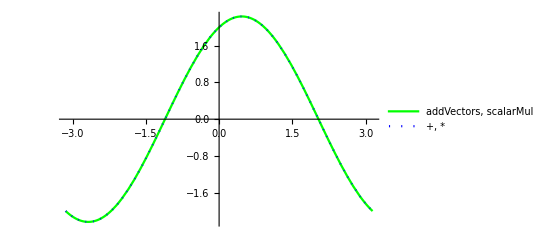

```mathematica
Plot[{(Sin~addVectors~(2~scalarMul~Cos))[t] , Sin[t] + 2 Cos[t]} , {t , -π , π} , PlotStyle->{Green , {Blue , Dotted}} , PlotLegends->{"addVectors, scalarMul" , "+, *"}]
```

```mathematica
(*UWAGA: nawias w (-2) jest konieczny.*)
```

```mathematica
smieszna = (Cos~addVectors~(Sin~addVectors~((-2)~scalarMul~Cos)))
```

Function[t$,Cos[t$]+Function[t$,Sin[t$]+Function[t$,-2 Cos[t$]][t$]][t$]]

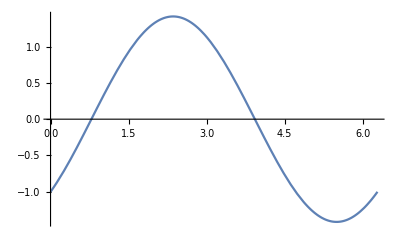

```mathematica
Plot[smieszna[t] , {t , 0 , 2π}]
```

## Układy równań liniowych, równania macierzowe, eliminacja Gaussa

Rozważmy układ równań (k jest parametrem):
x-2 y=2
-4 x+8 y=k
Aby rozwiązać ten układ równań możemy:

mnozyć dowolne równanie przez liczbę

dodawać jedno równanie do innego

Można się łatwo przekonać, że te operacje możemy przetłumaczyć na język macierzowy. Rozwiązanie tego układu równań jest równoważne rozwiązaniu równania macierzowego w postaci:
(1 | -2
-4 | 8)(x
y)=(2
k)
Operacje mnożenia równania przez liczbę oraz dodawanie jednego równania do drugiego można przetłumaczyć na operacje mnożenia wiersza (mulRow) oraz dodawania jednego wiersza do drugiego (addRow) dla połączonej macierzy:
(1 | -2 | 2
-4 | 8 | k)

```mathematica
(*Operacja tworzenia macierzy połączonej. "a" to główna macierz równania, "b" to wyrazy wolne. UWAGA wurazy wolne muszą być dodatkowo otoczone listą np zamiast {2 , k} należy stosować {{2 , k}}:*)
makeJoined[a_ , b_]:= Transpose[Join[Transpose[a] , b]];
(*Mnożenie wiersza "row" macierzy "joined" przez liczbę "num":*)
mulRow[row_ , num_][joined_]:=Join[joined[[1;;row-1]],{num joined[[row]]},joined[[row+1;;]]];
(*Dodawanie wiersza "from" macierzy "joined" do wiersza "to":*)
addRow[from_, to_][joined_]:=Join[joined[[1;;to-1]],{joined[[from]]+joined[[to]]},joined[[to+1;;]]];
(*Dodawanie wiersza "from" macierzy "joined", przemnożonego dodatkowo przez "mul", do wiersza "to":*)
addRow[from_ ,mul_, to_][joined_]:=Join[joined[[1;;to-1]],{mul joined[[from]]+joined[[to]]},joined[[to+1;;]]];
```

Na początek prosty układ równań :

```mathematica
Clear[a , b];
```

```mathematica
a = {{1 , 2} , {3 , 4}};
b = {5 , 6};
```

```mathematica
(*UWAGA: pamiętać o {}*)
makeJoined[a , {b}]//MatrixForm
```

(1 | 2 | 5
3 | 4 | 6)

```mathematica
(*robimy porządek i mnożymy drugi wiersz przez 1/3*)
mulRow[2 , 1/3][%]//MatrixForm
```

(1 | 2 | 5
1 | 4/3 | 2)

```mathematica
(*możemy do drugiego rzędu dodać pierwszy, pomnożony dodatkowo przez -1*)
addRow[1 , -1 , 2][%]//MatrixForm
```

(1 | 2 | 5
0 | -2/3 | -3)

```mathematica
(*robimy porządek, przemnażamy drugi rząd przez -3/2*)
mulRow[2 , -3/2][%]//MatrixForm
```

(1 | 2 | 5
0 | 1 | 9/2)

```mathematica
(*na diagonali mamy jedynki, problem w zasadzie rozwiązany ale pozbędziemy się jeszcze dwójki. Dodajemy do pierwszego rzędu, rząd drugi przemnożony przez -2*)
addRow[2 , -2 , 1][%]//MatrixForm
```

(1 | 0 | -4
0 | 1 | 9/2)

Teraz widać, że x = -4 oraz y = 9/2. Można sprawdzić czy rozwiązanie się zgadza:

```mathematica
a.{-4 , 9/2}
```

{5,6}

```mathematica
b
```

{5,6}

Teraz można spróbować znaleźć macierz odwrotną. Tutaj będzie mniej komentarza. Proszę się zastanowić jak to działa.

```mathematica
makeJoined[a , IdentityMatrix[2]]//MatrixForm
```

(1 | 2 | 1 | 0
3 | 4 | 0 | 1)

```mathematica
mulRow[2 , 1/3][%]//MatrixForm
```

(1 | 2 | 1 | 0
1 | 4/3 | 0 | 1/3)

```mathematica
addRow[1 , -1 , 2][%]//MatrixForm
```

(1 | 2 | 1 | 0
0 | -2/3 | -1 | 1/3)

```mathematica
mulRow[2 , -3/2][%]//MatrixForm
```

(1 | 2 | 1 | 0
0 | 1 | 3/2 | -1/2)

```mathematica
addRow[2 , -2 , 1][%]//MatrixForm
```

(1 | 0 | -2 | 1
0 | 1 | 3/2 | -1/2)

```mathematica
aInv = %[[;; , 3;;]];
```

```mathematica
aInv//MatrixForm
```

(-2 | 1
3/2 | -1/2)

aInv jest macierzą odwrotną do a:

```mathematica
aInv.a//MatrixForm
```

(1 | 0
0 | 1)

```mathematica
aInv.b
```

{-4,9/2}

Teraz nieco bardziej skomplikowany problem:

```mathematica
Clear[a , b]
```

```mathematica
a = {{1 , -2},{-4 , 8}};
```

```mathematica
b = {2 , k};
```

```mathematica
makeJoined[a , {b}]//MatrixForm
```

(1 | -2 | 2
-4 | 8 | k)

```mathematica
mulRow[2 , -1/4][%]//MatrixForm
```

(1 | -2 | 2
1 | -2 | -k/4)

```mathematica
addRow[1 , -1 , 2][%]//MatrixForm
```

(1 | -2 | 2
0 | 0 | -2-k/4)

Co to oznacza? Kiedy to równanie ma rozwiązanie? Jak to zależy od wartości “k”? Jaki jest rząd macierzy w zależności od k? Rząd macierzy “a”:

```mathematica
a//MatrixForm
```

(1 | -2
-4 | 8)

```mathematica
mulRow[2 , -1/4][%]//MatrixForm
```

(1 | -2
1 | -2)

```mathematica
addRow[1 , -1 , 2][%]//MatrixForm
```

(1 | -2
0 | 0)

```mathematica
(*a = {{1 , 1 , -1} , {3  , -5 , 13} , {1 , -2 , 5}};*)
```

```mathematica
(*b = {-2 , 18 , k};*)
```

## Przestrzeń wektorowa rozpinana przez sin, cos. Równania różniczkowe.

```mathematica
Clear[a , b];
```

Najpierw pełne rozwiązanie jednego z równań:

```mathematica
DSolve[D[x[t] , {t , 2}] - D[x[t] , t] - x[t]==Cos[t] , x[t] , t]
```

{{x[t]→ⅇ^((1/2-(√5)/2) t) C[1]+ⅇ^((1/2+(√5)/2) t) C[2]+(4 (2 Cos[t]+Sin[t]))/((-5+√5) (5+√5))}}

Będziemy szukać szczególnego rozwiązania w postaci :

```mathematica
x[t_]:=a Sin[t] + b Cos[t];
```

```mathematica
D[x[t] , t ]
```

a Cos[t]-b Sin[t]

```mathematica
D[x[t] , {t , 2}]
```

-b Cos[t]-a Sin[t]

W postaci wektorowej x = (a , b),macierz reprezentująca różniczkowanie:

```mathematica
ddt={{0 , -1} , {1 , 0}};
```

```mathematica
ddt.{a , b}
```

{-b,a}

macierz reprezentująca podwójne różniczkowanie:

```mathematica
ddt.ddt.{a , b}
```

{-a,-b}

Wskazówka : teraz wystarczy ułożyć odpowiedni układ równań liniowych i go rozwiązać ...